# Spectrum Processing

## Last Updated: 2023/04/03

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

## Parameters

```mathematica
(*ion parameters*)
carrierFreqMHz=102.3356;
countsSignal=170;
countsNoise=18;
```

```mathematica
(*search parameters*)
ωKnown=<|
0.700->"Axial 1",
1.216->"Axial 2",
1.138->"RF 2",
1.394->"RF 1",
1.363->"EGGS 2",
1.595->"EGGS 1"
|>;
ωOrder=3;
ωTolerance=0.05;
```

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2024-03\\2024-03-27";
```

```mathematica
(*select by RID*)
ridDJ=52975;
```

## Setup

## Values

```mathematica
(*converting ftw to frequency*)
ftwToMHz=10^3/(2^32-1);
```

```mathematica
(*count discrimination*)
countsThreshold=N[countsSignal/Log[1+countsSignal/countsNoise]];
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
```

## Functions

### General

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],"none",EmitSound[soundDJ]
];
];
```

### Peak Finding

```mathematica
(*return sorted peaks from a 2-D list of {x, y}*)
CalculatePeaks[dataset_,σ_:0.1,s_:0,t_:0]:=Module[
{datasetPeaks=FindPeaks[dataset[[;;,2]],σ,s,t]},
(*ensure dataset indices from findpeaks are integers*)
datasetPeaks[[;;,1]]=dataset[[Round[datasetPeaks[[;;,1]]],1]];
Return[Reverse[SortBy[datasetPeaks,Last]]]
];
```

### Dataset Processing

```mathematica
(*process spectrum dataset*)
ProcessSpectrumDataset[filename_]:=Module[
{
(*actual data*)
dataRaw=Import[filename,{"/datasets/results"}],
dataProcessed
},

(*process dataset*)
dataRaw[[;;,1]]=(dataRaw[[;;,1]]*ftwToMHz-carrierFreqMHz)*2;

(*group and threshold counts into probability*)
dataProcessed=GroupBy[dataRaw,First->Last,Mean@HeavisideTheta[#-countsThreshold]&]//KeySort;
(*additional processing*)
dataProcessed=1-dataProcessed//N;

(*clean up mess*)
Remove[dataRaw];
ClearSystemCache[];
ClearInOut[];

(*return dataset*)
Return[Transpose[{Keys[#],Values[#]}]&[dataProcessed]];
];
```

## Import

## Get Filepath

```mathematica
(*select file with give RID from all subdirectories*)
filenamesAll=FileNames["*.h5",directoryString,Infinity];
(*get only first file that matches*)
filenameDJ=First@Select[filenamesAll,StringContainsQ[#,ToString[ridDJ]]&];
```

## Import & Process Dataset

```mathematica
(*import and process data*)
dataset=ProcessSpectrumDataset[filenameDJ];
```

## Process

## Find Peaks

```mathematica
(*find peaks*)
peakList=CalculatePeaks[dataset,10,0,0.1];
```

## Guess Modes

```mathematica
(*generate combination mode frequencies*)
ωCoefficients=Tuples[Range[-ωOrder,ωOrder],Length[ωKnown]];
ωCoefficients=Select[ωCoefficients,0<Total[Abs/@#]<=ωOrder&];
ωGuess=AssociationThread[ωCoefficients,ωCoefficients.Keys[ωKnown]];
```

```mathematica
(*find likely combination modes*)
ωCandidates=Nearest[ωGuess,#,{1,ωTolerance}]&/@peakList[[;;,1]];
ωCandidates=%/.{{}->{{0,0,0}}};
```

## Plot

## Spectrum Figures

```mathematica
(*create spectrum plot*)
spectrumPlot=ListLinePlot[
dataset,
PlotRange->Full,
FrameLabel->{ 
{Style["Population (D_(5/2))",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Spectrum - RIDs: "<>ToString[ridDJ],{Black,Directive[15]}]}
}
];
```

## Peak Figures

```mathematica
(*format peak data for plotting*)
peakPlotData=MapThread[
Labeled[#1,#2,Left]&,
{peakList,(First/@ωCandidates).(Values[Subscript["n",#]&/@ωKnown])}
];
(*format peak plot*)
peakPlot=ListPlot[
peakPlotData,
PlotStyle->Directive[
Orange,
PointSize[0.01]
]
];
```

```mathematica
(*formatted data for peak table*)
peakTableData=MapThread[
{#1,#2,#3,Abs[#1-#2]/#1*100}&,
{
peakList[[;;,1]],
Apply[ωGuess,ωCandidates,{1}],
(First/@ωCandidates).(Values[Subscript["n",#]&/@ωKnown])
}
];
peakTableHeadings={
"Peak "<>ToString[#]&/@Range[Length[peakTableData]],
{"Actual Frequency (MHz)", "Expected Frequency","Mode","Error (%)"}
};
```

```mathematica
(*create peak table*)
peakTable=Style[Labeled[
TableForm[
peakTableData,
TableHeadings->peakTableHeadings,
TableAlignments->{Right,Right,Left, Right}
],
"Spectrum Peaks",
Top
],
Black,Background->White
];
```

## Summary Figure

```mathematica
(*combine into ultimate plot*)
summaryPlot=TableForm[
{
Show[spectrumPlot,peakPlot],
peakTable
},
TableDirections->Row
];
```

## Summary

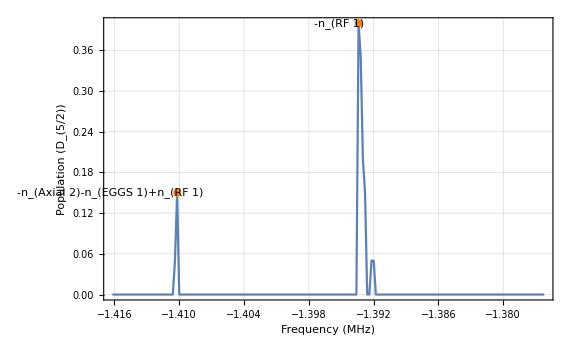
-Graphics- |  | Actual Frequency (MHz) | Expected Frequency | Mode | Error (%)
Peak 1 | -1.3934 | -1.394 | -n_(RF 1) | -0.0430468
Peak 2 | -1.4102 | -1.417 | -n_(Axial 2)-n_(EGGS 1)+n_(RF 1) | -0.482212Spectrum Peaks

```mathematica
summaryPlot
```